Fermi Arc of PTB in Momentum Space

```mathematica
Clear[Lx,Ly,A,
sx2d,SX2D,sx2dp,SX2DP,
sy2d,SY2D,sy2dp,SY2DP,
cx2d,CX2D,cx2dp,CX2DP,
cy2d,CY2D,cy2dp,CY2DP,
cons,Cons]
```

```mathematica
(**Change the system size here **)
```

```mathematica
Lx=32;
Ly=32;
A=Lx*Ly;
```

```mathematica
(**-----------------Define the sine and cosine matrices for the parent square lattice--------------------**)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sx2d[i_Integer,j_Integer]=0;

Do[Do[{sx2d[j+k Lx,j+1+k Lx]=-I/2,sx2d[j+1+k Lx,j+k Lx]=I/2},{j,1,Lx-1}],{k,0,Ly-1}]

SX2D=Table[sx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sx2dp[i_Integer,j_Integer]=0;

Do[{sx2dp[(k+1)Lx,1+k Lx]=-I/2,sx2dp[1+k Lx,(k+1)Lx]=I/2},{k,0,Ly-1}]

SX2DP=Table[sx2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sy2d[i_Integer,j_Integer]=0;

Do[Do[{sy2d[k Lx+j,(k+1)Lx+j]=-I/2,sy2d[(k+1)Lx+j,k Lx+j]=I/2},{j,1,Lx}],{k,0,Ly-2}]

SY2D=Table[sy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sy2dp[i_Integer,j_Integer]=0;

Do[{sy2dp[(Ly-1)Lx+j,j]=-I/2,sy2dp[j,(Ly-1)Lx+j]=I/2},{j,1,Lx}]

SY2DP=Table[sy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cx2d[i_Integer,j_Integer]=0;

Do[Do[{cx2d[j+k Lx,j+1+k Lx]=1/2,cx2d[j+1+k Lx,j+k Lx]=1/2},{j,1,Lx-1}],{k,0,Ly-1}]

CX2D=Table[cx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cx2dp[i_Integer,j_Integer]=0;

Do[{cx2dp[(1+k)Lx,1+k Lx]=1/2,cx2dp[1+k Lx,(1+k)Lx]=1/2},{k,0,Ly-1}]

CX2DP=Table[cx2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cy2d[i_Integer,j_Integer]=0;

Do[Do[{cy2d[k Lx+j,(k+1)Lx+j]=1/2,cy2d[(k+1)Lx+j,k Lx+j]=1/2},{j,1,Lx}],{k,0,Ly-2}]

CY2D=Table[cy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cy2dp[i_Integer,j_Integer]=0;

Do[{cy2dp[(Ly-1)Lx+j,j]=1/2,cy2dp[j,(Ly-1)Lx+j]=1/2},{j,1,Lx}]

CY2DP=Table[cy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------- Lattice model for a constant matrix for the parent square lattice---------------*)
```

```mathematica
cons[i_Integer, j_Integer]:=0

Do[{cons[i,i]=1},{i,1,A}]

Cons=Table[cons[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[σ0,σ1,σ2,σ3,HamiltonianWSM]
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
```

```mathematica
HamiltonianWSM[t_,t0_,m_,tz_,kz_,α_]:=t*(KroneckerProduct[SX2D+α*SX2DP,σ1]+KroneckerProduct[SY2D+α*SY2DP, σ2])+KroneckerProduct[2*Cons-2t0*(CX2D+CY2D+α*CX2DP+α*CY2DP),σ3]+KroneckerProduct[(tz *Cos[kz]-m)*Cons,σ3]
```

```mathematica
(*--------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[val,vec,ValVecAHI,ValAHI,ValAHIRange]
```

```mathematica
{val,vec}=Eigensystem[HamiltonianWSM[1.,0.5,4,1,π/2-0.5,0]];
```

```mathematica
ValVecAHI=SortBy[Transpose[{val,vec}],First];
```

```mathematica
ValAHI=Table[{j,Re[ValVecAHI[[j,1]]]},{j,1,2A}];
```

```mathematica
ValAHIRange=Table[ValAHI[[j,2]],{j,1,2 A}];
```

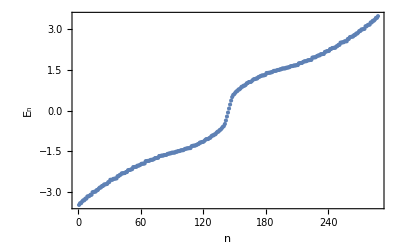

```mathematica
Show[ListPlot[ValAHI,Frame-> True,Axes-> False,PlotRange-> {{0,2A},{Min[ValAHIRange],Max[ValAHIRange]}}],(**Plot[0,{x,0,2A},PlotStyle-> Red],**)BaseStyle-> 14,FrameStyle-> Black,FrameLabel-> {"n","E_n"}]
```

```mathematica
(** Generate a vector where values of kz for which we will diagonalize the Hamiltonian is stored **)
```

```mathematica
Clear[kzVector]
```

```mathematica
kzVector = N@Subdivide[-π,π,50]
```

{-3.14159,-3.01593,-2.89027,-2.7646,-2.63894,-2.51327,-2.38761,-2.26195,-2.13628,-2.01062,-1.88496,-1.75929,-1.63363,-1.50796,-1.3823,-1.25664,-1.13097,-1.00531,-0.879646,-0.753982,-0.628319,-0.502655,-0.376991,-0.251327,-0.125664,0.,0.125664,0.251327,0.376991,0.502655,0.628319,0.753982,0.879646,1.00531,1.13097,1.25664,1.3823,1.50796,1.63363,1.75929,1.88496,2.01062,2.13628,2.26195,2.38761,2.51327,2.63894,2.7646,2.89027,3.01593,3.14159}

```mathematica
aaaaa=Dimensions[kzVector][[1]]
```

51

```mathematica
DensityVector = {};
```

```mathematica
Do[{Clear[H,val,vec,ValVecAHI,singledatDensityVector],
H = HamiltonianWSM[1.,0.5,4,1,kzVector[[p]],0],
{val,vec}=Eigensystem[H],
ValVecAHI=SortBy[Transpose[{val,vec}],First],
reqVector = ValVecAHI[[A]][[2]],
singledatDensityVector = Abs[reqVector]*Abs[reqVector],
Do[Do[DensityVector=Append[DensityVector,{i,j,kzVector[[p]],singledatDensityVector[[2(i + (j-1)*Lx )]]+singledatDensityVector[[2(i + (j-1)*Lx)-1]]}],{i,1,Lx}],{j,1,Ly}]},{p,1,aaaaa}]
```

```mathematica
Clear[datDiracIns,colorfunc,rng,P1]
```

```mathematica
datDiracIns=DensityVector;
```

```mathematica
colorfunc=Function[{v,vmax},Hue[0.5+0.5*v/vmax,1,1.0-0.3 v/vmax,(v/vmax)]];
```

```mathematica
rng={0,Max[#]}&@datDiracIns[[All,4]];
```

```mathematica
rng[[2]]
```

0.0178754

```mathematica
P1=BarLegend[{colorfunc[#,rng[[2]]]&,{0,rng[[2]]}},LabelStyle->{Black,FontSize-> 15},Ticks-> {{0,"0.0"},{rng[[2]]/2,"0.89"},{rng[[2]]-10^-4,"1.78"}}]
```

```mathematica
Graphics3D[{PointSize[0.03],colorfunc[#[[4]],rng[[2]]],Point[#[[1;;3]]]}&/@datDiracIns,Axes->True,BoxRatios->1,BoxStyle->Directive[Thickness[0.0075]],AxesLabel->{"x","y","k_z"},BaseStyle->15,Ticks-> {{{1,"1"},{Lx,"32"}},{{1,"1"},{Ly,"32"}},{{-π,"-π"},{-π/2,"-π/2"},{π/2,"π/2"},{π,"π"}}},PlotRange->{{1,Lx},{1,Ly},{-π,π}},ImageSize->400]
```

-Graphics3D-

```mathematica
(** Export["MixedBlochWannierFermiArc32x32m=4.dat",DensityVector] **)
```

```mathematica
(**----Clear memory for PTB----**)
```

```mathematica
Clear[val,vec,ValVecAHI,ValAHI,ValAHIRange]
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------------quasicrystal--------------------------*)
```

```mathematica
Clear[Sitelocation,FlatSite,Sites, LineUp,LineDn]
```

```mathematica
Sitelocation=Table[{i,j},{i,1,Lx},{j,1,Ly}];
```

```mathematica
FlatSite=Flatten[Sitelocation];
```

```mathematica
NOrbitals=Dimensions[FlatSite][[1]]
```

2048

```mathematica
Sites=Table[{FlatSite[[i]],FlatSite[[i+1]]},{i,1,NOrbitals,2}];
```

```mathematica
(**--Equations for the two red lines--**)
```

```mathematica
(** Comment/Uncomment the rational and irrational equations accordingly **)
```

```mathematica
(**-------Irrational-------**)
```

```mathematica
LineUp[x_]:=((1+√5)/2)^-1*(x-1)+8
LineDn[x_]:=((1+√5)/2)^-1*(x-2)+6
```

```mathematica
(**-------Rational-------**)
```

```mathematica
(** LineUp[x_]:=(2/3)(x-1)+8
LineDn[x_]:=(2/3)*(x-2)+6 **)
```

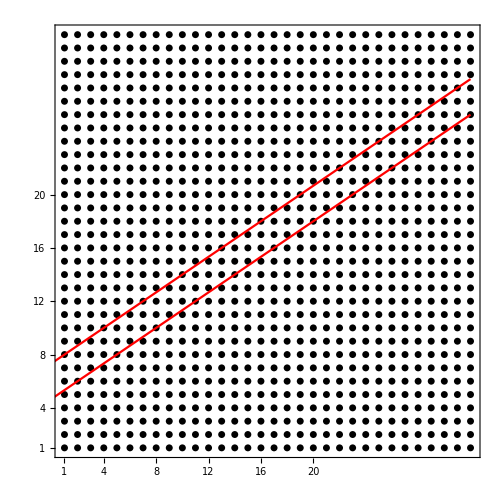

```mathematica
Show[ListPlot[Sites,PlotStyle-> {Black,PointSize[0.01]},Frame-> True,Axes-> False,PlotRange-> {{0.9,Lx+0.1},{0.9,Ly+0.1}}],
Plot[LineUp[x],{x,0,Lx},PlotStyle-> Red],
Plot[LineDn[x],{x,0,Lx},PlotStyle-> Red],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,
ImageSize-> 500,AspectRatio-> 1
]
```

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[Fibonup,Fibondown,TotalFibon,XList, YList, XListKron, YListKron]
```

```mathematica
(**-----We want to count points inside the area of interest, store them in FibonupNew, and sort them into Fibonup-----**)
```

```mathematica
Clear[FibonupNew]
FibonupNew={};
```

```mathematica
(**---Points on the lines are not taken---**)
```

```mathematica
(**---That is why we calculate Floor[]+1 instead of Ceiling, and Ceiling[]-1 instead of Floor---**)
```

```mathematica
Do[Do[FibonupNew=Append[FibonupNew,x+(y-1)*Lx],{y,Max[1,Floor[LineDn[x]]+1],Min[Ly,Ceiling[LineUp[x]]-1]}],{x,1,Lx}]
```

```mathematica
FibonupNew;
```

```mathematica
Fibonlist=Sort[FibonupNew]
```

{161,193,194,195,226,227,228,259,260,261,262,293,294,295,326,327,328,329,360,361,362,393,394,395,396,427,428,429,460,461,462,463,494,495,496,527,528,529,530,561,562,563,594,595,596,597,628,629,630,661,662,663,664,695,696,697,728,729,730,731,762,763,764,795,796,797,798,829,830,831,862,863,864,896}

```mathematica
YList = Ceiling[Fibonlist/Lx];
```

```mathematica
XList = Fibonlist - (YList - 1)Lx;
```

```mathematica
(**Check that the list is correct**)
```

```mathematica
XList + (YList-1)*Lx - Fibonlist
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
XListKron = Flatten[KroneckerProduct[XList,{1,1}],2];
```

```mathematica
YListKron = Flatten[KroneckerProduct[YList,{1,1}],2];
```

```mathematica
(**----Group the orbitals in the sites in Fibonlist ---**)
```

```mathematica
Fibonup = 2 * Fibonlist -1;
```

```mathematica
Fibondown = 2 * Fibonlist;
```

```mathematica
(**-- Fibondown=Table[Fibonlist[[j]]+A,{j,1,Dimensions[Fibonlist][[1]]}]; --**)
```

```mathematica
TotalFibon=Flatten[{Fibonup,Fibondown}];
```

```mathematica
TotalFibon = Sort[TotalFibon]
```

{321,322,385,386,387,388,389,390,451,452,453,454,455,456,517,518,519,520,521,522,523,524,585,586,587,588,589,590,651,652,653,654,655,656,657,658,719,720,721,722,723,724,785,786,787,788,789,790,791,792,853,854,855,856,857,858,919,920,921,922,923,924,925,926,987,988,989,990,991,992,1053,1054,1055,1056,1057,1058,1059,1060,1121,1122,1123,1124,1125,1126,1187,1188,1189,1190,1191,1192,1193,1194,1255,1256,1257,1258,1259,1260,1321,1322,1323,1324,1325,1326,1327,1328,1389,1390,1391,1392,1393,1394,1455,1456,1457,1458,1459,1460,1461,1462,1523,1524,1525,1526,1527,1528,1589,1590,1591,1592,1593,1594,1595,1596,1657,1658,1659,1660,1661,1662,1723,1724,1725,1726,1727,1728,1791,1792}

```mathematica
NOrbitalsQuasi=Dimensions[TotalFibon][[1]]
```

148

```mathematica
NOrbitalsQuasi/2
```

74

```mathematica
NOrbitalsOutside = NOrbitals-NOrbitalsQuasi
```

1900

```mathematica
PercentageDataIn = N[NOrbitalsQuasi/(2*A)]
```

0.0722656

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[F1,a]
```

```mathematica
F1=Table[i,{i,1,2*A}];
```

```mathematica
Dimensions[F1]
```

{2048}

```mathematica
a= Complement[F1, TotalFibon];
```

```mathematica
(**-------------------------------**)
```

```mathematica
Clear[Fibon1D,largestX]
```

```mathematica
Fibon1D=Table[{ii,0},{ii,1,NOrbitalsQuasi/2}]
```

{{1.,0},{1.9245,0},{2.4792,0},{3.4037,0},{4.3282,0},{4.8829,0},{5.8074,0},{6.7319,0},{7.2866,0},{8.2111,0},{9.1356,0},{9.6903,0},{10.6148,0},{11.5393,0},{12.094,0},{13.0185,0},{13.943,0},{14.4977,0},{15.4222,0},{16.3467,0},{16.9014,0},{17.8259,0},{18.7504,0},{19.3051,0},{20.2296,0},{21.1541,0},{21.7088,0},{22.6333,0},{23.5578,0},{24.1125,0},{25.037,0},{25.9615,0},{26.5162,0},{27.4407,0},{28.3652,0},{28.9199,0},{29.8444,0},{30.7689,0},{31.3236,0},{32.2481,0},{33.1726,0},{33.7273,0},{34.6518,0},{35.5763,0},{36.131,0},{37.0555,0},{37.98,0},{38.5347,0},{39.4592,0},{40.3837,0},{40.9384,0},{41.8629,0},{42.7874,0},{43.3421,0},{44.2666,0},{45.1911,0},{45.7458,0},{46.6703,0},{47.5948,0},{48.1495,0},{49.074,0},{49.9985,0},{50.5532,0},{51.4777,0},{52.4022,0},{52.9569,0},{53.8814,0},{54.8059,0},{55.3606,0},{56.2851,0},{57.2096,0},{57.7643,0},{58.6888,0},{59.6133,0}}

```mathematica
largestX=Ceiling[Fibon1D[[Dimensions[Fibon1D][[1]],1]]]
```

60

```mathematica
(**-------------------------------**)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[TabFibNew, TabRenorEnergies]
```

```mathematica
TabFibNew={}
```

{}

```mathematica
TabRenorEnergies={}
```

{}

```mathematica
Do[{Clear[HTrial,Hfbfb,HFBFB,H2d2d,H2D2D,H2dfb,H2DFB,Hfb2d,HFB2D],
HTrial=HamiltonianWSM[1.,1.,0,1,kzVector[[p]],0],
(*---------------------------------------------------------*)
Hfbfb[i_Integer,j_Integer]=0,
Do[
Do[
Hfbfb[i,j]=HTrial[[TotalFibon[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsQuasi}
],
{j,1,NOrbitalsQuasi}
],
HFBFB=Table[Hfbfb[i,j],{i,1,NOrbitalsQuasi},{j,1,NOrbitalsQuasi}],
(*---------------------------------------------------------*)
H2d2d[i_Integer,j_Integer]=0,
Do[
Do[
H2d2d[i,j]=HTrial[[a[[i]],a[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsOutside}
],
H2D2D=Table[H2d2d[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsOutside}],
(*------------------------------------------------------*)
H2dfb[i_Integer,j_Integer]=0,

Do[
Do[
H2dfb[i,j]=HTrial[[a[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsQuasi}
],
H2DFB=Table[H2dfb[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsQuasi}],
(*-------------------------------------------------*)
Hfb2d[i_Integer,j_Integer]=0,

Do[
Do[
Hfb2d[i,j]=HTrial[[TotalFibon[[i]],a[[j]]]],
{i,1,NOrbitalsQuasi}
],
{j,1,NOrbitalsOutside}
],
HFB2D=Table[Hfb2d[i,j],{i,1,NOrbitalsQuasi},{j,1,NOrbitalsOutside}],

(*---------------------------------------------------------------------------------------------------------------------------------*)
Clear[HFibonRenor,ValueFibon,VecFibon,ValVecFibon,ValFibon],
HFibonRenor=HFBFB-(HFB2D.Inverse[H2D2D].H2DFB),
(**------Check that HFibonRenor is Hermitian------**)
(**--- ConjugateTranspose[HFibonRenor] - HFibonRenor//Chop ---**)
{ValueFibon,VecFibon}=Eigensystem[HFibonRenor],
ValVecFibon=SortBy[Transpose[{ValueFibon,VecFibon}],First],
ValFibon=Table[{j,ValVecFibon[[j,1]]},{j,1,NOrbitalsQuasi}]//Chop,
(*Show[ListPlot[ValFibon,Frame-> True,Axes-> False,BaseStyle-> 16,PlotStyle-> Black,FrameStyle-> Black(**,PlotRange->{{0,84},{-2,2}}**)],Plot[0,{x,-100,100},PlotStyle-> Red]]*)
(** without dislocation -1 OBC **)
(** without dislocation +1 OBC **)
OnlyEigenvalue=Table[ValFibon[[j,2]],{j,1,NOrbitalsQuasi}],
Tr[OnlyEigenvalue]//Chop,
percentageOfOrbitalsInside = N[NOrbitalsQuasi/(2*A)],
NSitesInside = NOrbitalsQuasi/2,
(*---------------------------------------------------------------------------------------------------------*)
(*---------------------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------------------------------------------------*)
(*-------------------------------------------------------------------------------------------------------------------------------------*)
ValFibon[[(NOrbitalsQuasi/2)+1,2]],
Clear[J,TabDataFibon,TDFibon],
J=NOrbitalsQuasi/2;,
TabDataFibon=Table[{Fibon1D[[i,1]],0,
Abs[ValVecFibon[[J,2,2i]]]^2+Abs[ValVecFibon[[J,2,2i-1]]]^2

+Abs[ValVecFibon[[J+1,2,2i]]]^2+Abs[ValVecFibon[[J+1,2,2i-1]]]^2

},{i,1,NOrbitalsQuasi/2}],
TDFibon=Flatten[TabDataFibon],
Do[TabFibNew = Append[TabFibNew,{TDFibon[[i]],kzVector[[p]],TDFibon[[i+2]]}],{i,1,3*NOrbitalsQuasi/2,3}],
Do[TabRenorEnergies = Append[TabRenorEnergies,{kzVector[[p]],OnlyEigenvalue[[i]]}],{i,1,NOrbitalsQuasi}]
},{p,1,aaaaa}]
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
TabFibNewNewFromPiby2Only = {};
```

```mathematica
Do[If[Abs[TabFibNew[[ii]][[2]]]<π/2,TabFibNewNewFromPiby2Only=Append[TabFibNewNewFromPiby2Only,TabFibNew[[ii]]]],{ii,1,Dimensions[TabFibNew][[1]]}]
```

```mathematica
(** Export["WSMTabfibnewdata_m4_up+8_dn+6Rationalm=0.dat",TabFibNew]; **)
```

```mathematica
(** Export["Fibon1Drational.dat",Fibon1D]; **)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```